```mathematica
SetDirectory[NotebookDirectory[]];Clear["Global`*"];
Get["../sources/KimberlingPoints.m"]; 
Get["../sources/TriangleExpressions.m"]; 
Get["../sources/KimberlingTrilinears1000.m"];
Get["../sources/ConicTools.m"];
```

```mathematica
(* 
Here we will be numerically exploring the following question. Let ABC be a triangle with incenter X1. Let Ea be the ellipse through X1 with foci B,C and build Eb and Ec cyclically.Denote as xA the intersection, other than I, of Eb and Ec,and cyclically xB and xC. Check that the lines A-xA, B-xB, C-xC concur. Is this point in ETC?
*)
(* Commands provided by the Kimberling repo are in green. *)
(* \
KimberlingTrilinears1000.m -> Barycentric coordinates of the forst 1000 points in ETC
TriangleExpressions.m -> Needs to be included always with KimberlingTrilinears files
KimberlingPoints.m -> Provides KimberlingCenter[] and KimberlingCenterB[].
*)
```

```mathematica
PA={31/3,(4 √35)/3}; PB={0,0}; PC={6,0}; (* set up the 6-9-13 triangle *)
```

```mathematica
(* Calculate ellipses *)
X1 =KimberlingCenter[1,PA,PB,PC];

(* 
ellipseFociPtEq[F1,F1,P] constructs a conic object for the ellipse with foci F1 and F2 which passes through P
It returns the matrix of the ellipse equation.
 *)
elc = ellipseFociPtEq[PA,PB,X1]//Simplify;
elb = ellipseFociPtEq[PC,PA,X1]//Simplify;
ela = ellipseFociPtEq[PB,PC,X1]//Simplify;

(* We use matrixToEq[] to convert the ellipse matrix form to equation form. *)
{EA, EB,EC}=ImplicitRegion[matrixToEq[#]==0,{x,y}]&/@{ela,elb,elc};

(* 
Select the other intersection point of the ellipses, not X1. 
*)
chorda=NSolve[matrixToEq[elb]==0 &&matrixToEq[elc]==0,{x,y}, Reals,WorkingPrecision->50];
xA = If[EuclideanDistance[X1,{x, y}/.chorda[[1]]]<10^-10,{x,y}/.chorda[[2]], {x, y}/.chorda[[1]]];

chordb=NSolve[matrixToEq[ela]==0 &&matrixToEq[elc]==0,{x,y}, Reals,WorkingPrecision->50];
xB = If[EuclideanDistance[X1,{x, y}/.chordb[[1]]]<10^-10,{x,y}/.chordb[[2]], {x, y}/.chordb[[1]]];

chordc=NSolve[matrixToEq[ela]==0 &&matrixToEq[elb]==0,{x,y}, Reals,WorkingPrecision->50];
xC = If[EuclideanDistance[X1,{x, y}/.chordc[[1]]]<10^-10,{x,y}/.chordc[[2]], {x, y}/.chordc[[1]]];

linea=lineEqPt[xA, PA]//Simplify;
lineb=lineEqPt[xB, PB]//Simplify;
linec=lineEqPt[xC, PC]//Simplify;
```

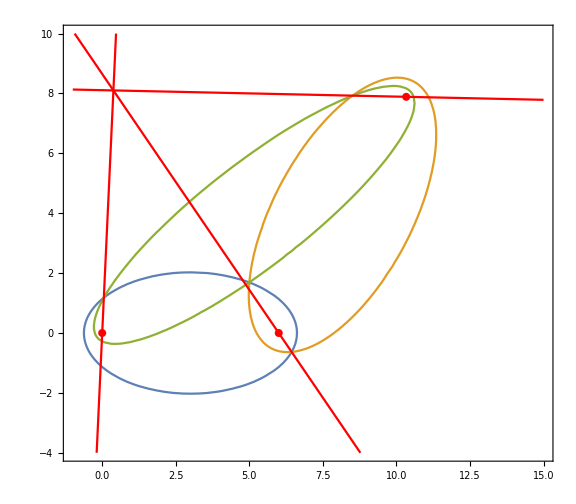

```mathematica
Show[
ContourPlot[{matrixToEq[ela]==0, matrixToEq[elb]==0,matrixToEq[elc]==0} ,
{x,-1,15},{y,-4,10},
AspectRatio->Automatic, ImageSize->Large, 
Epilog->{PointSize[0.01],Red,Point[#]&/@{PA, PB, PC}}
], 
ContourPlot[{linea==0, lineb==0, linec==0} ,{x,-1,15},{y,-4,10}, ContourStyle->Red]
]
```

```mathematica
cConcurrencyMatrix[linea,lineb,linec] (* check concurrency *)
```

-5.497515468183866007278213943086992638608738044×10^-57

```mathematica
pointX=findIntersections[linea,lineb] (* find coordinates of intersection point *)
```

{0.3810278815303058166206870775310326275256284658,8.101636958113357263297620406376439908336067829}

```mathematica
Get["../sources/EtcCheckNumbers.m"];
```

```mathematica
(* Check against ETC coordinates database, which is stored in EtcCheckNumbers*)
MinimalBy[Value]@((Abs[#-pointX[[2]]])&/@EtcCheckNumbers)
```

<|X46705→0.|>